```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/hierarchical chain/

```mathematica
(* Thickness *)
th=0.003;
```

## Diagonalisation directe

### Energy bands

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* bout élémentaire du Hamiltonien périodique *)
Clear[h];
h[n_,k_]:=Block[{tbl,ar},
(* bout libre *)
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+=Transpose[ar];
(* bout périodique *)
ar+=SparseArray[{{1,2^n}->Exp[2^n I k]t[2^(n-1)],{2^n,1}->Exp[- 2^n I k]t[2^(n-1)]}]//Normal
]
```

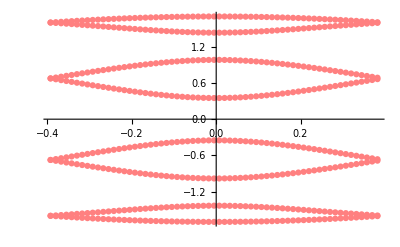

```mathematica
(* energy bands *)
Block[{v=.9,r=.5,listk,dk=.1,i=3,listEk,listH,l},
dk=dk/2^i;
listk=Range[-Pi/2^i,Pi/2^i,dk];
listH=ParallelMap[h[i,#]&,listk];
listEk=ParallelMap[Sort[Eigenvalues[#]]&,listH];
l=MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}];
ListPlot[l,PlotStyle->Directive[Pink]]
]
```

### Wavefunctions

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* non periodic part of the Hamiltonian *)
Clear[h];
(* permits us to pass list of arguments to h *)
SetAttributes[h,Listable];
(* we ARBITRARILY set the period to 1, ie we make the change 2^n k -> k *)
h[n_,k_]:=Block[{tbl,ar},
(* bout libre *)
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+=Transpose[ar];
(* bout périodique *)
ar+=SparseArray[{{1,2^n}->Exp[I k]t[2^(n-1)],{2^n,1}->Exp[- I k]t[2^(n-1)]}]//Normal
]
```

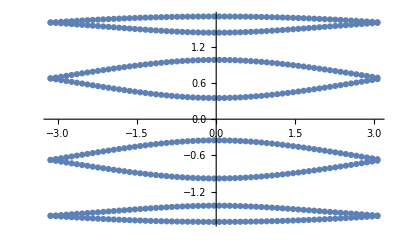

```mathematica
(* energy bands *)
Block[{v=.9,r=.5,listk,dk=.1,i=3,listEk,listH,l},
listk=Range[-Pi,Pi,dk];
listH=h[i,listk];
listEk=ParallelMap[Sort[Eigenvalues[#]]&,listH];
l=Flatten[MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}],1];
ListPlot[l]
]
```

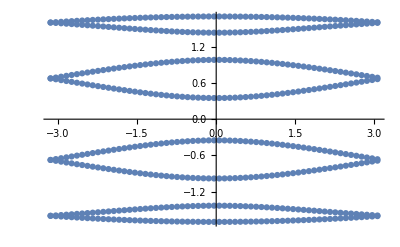

```mathematica
(* wavefunctions *)
Block[{v=.9,r=.5,listk,dk=.1,i=3,es,listEk,listWF,l},
listk=Range[-Pi,Pi,dk];
es=ParallelMap[Eigensystem,h[i,listk]];
{listEk,listWF}={#[[1]]&/@es,#[[2]]&/@es};
l=Flatten[MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}],1];
ListPlot[l]
]
```